# Numerical ODE Solvers

## Design Principle(s)

A good “black box” ODE solver should automatically efficiently compute accurate approximations to a broad range of ODEs.  Most such solvers ODE solvers solve 1st order systems.  As we have seen, both Matlab and Python require the user to reduce a general system of ODEs to a system of first order ODEs.  We are going to see how some families of solvers are defined and implemented.  Our n-dimensional IVP 
	y'=f(t,y)  and y(0)=y_0
is defined by the function f:ℝ×ℝ^n→ℝ^n and the initial condition y_0.

## Euler’s Method

We learned the simplest ODE solver in Calculus I.   The standard presentation is to substitute the approximation 
	y'(t)≈(y(t+h)-y(t))/h
for some small into the ODE to get
	(y(t+h)-y(t))/h=f(t,y(t)) 
and rearrange to get
	y(t+h)≈y(t)+h f(t,y(t)).
With a fixed small step size h this allows us to generate approximate values of y_k at the sequence of equally spaced t-value t_k=k h.

The code is pretty simple!

{{0.1,0.,1.},{0.1,0.1,1.1},{0.1,0.2,1.21},{0.1,0.3,1.331},{0.1,0.4,1.4641},{0.1,0.5,1.61051},{0.1,0.6,1.77156},{0.1,0.7,1.94872},{0.1,0.8,2.14359},{0.1,0.9,2.35795},{0.1,1.,2.59374}}

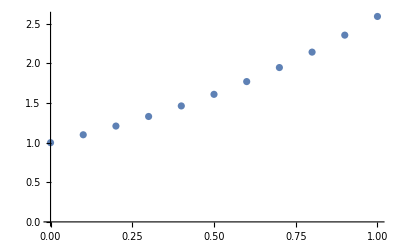

```mathematica
EulerStep[f_][{h_,t_,y_}]:={h,t+h,y+h f[t,y]}

f[t_,y_]:=y
h=0.1; t0=0.0; y0=1.0; EulerSteps=10;
EulerData=NestList[EulerStep[f],{h,t0,y0},EulerSteps]
ListPlot[ EulerData⟦All,2;;3⟧]
```

Fixed step-size Euler does not fit our “Design Principles” because we have no idea if the answer is accurate and we have no idea if we picked a reasonable step size h.  What we really want is some way to automatically tune the step size to the solution of the ODE.  This is not as hard as it sounds!

## Euler’s Method (Alternate Derivation) and Taylor Methods

Another way to motivate Euler’s method is to look at the ODE
	y'(t)=f(t,y(t))
and say use the linear approximation
	y(t_k+h)≈y(t_k)+h y'(t_k)=y(t_k)+h f(t_k,y(t_k))
writing h_k for the size of step k, and t_k and y_k for the approximation generated this way we have
	t_(k+1) | = | t_k | + | h_k
y_(k+1) | = | y_k | + | h_k f(t_k,y_k)
h_(k+1) | = | ? |   |  
With some way of choosing the step sizes we would get an approximate solution values {y_k} at the points {t_k}.

The quadratic approximation
	y(t_k+h)≈y(t_k)+h y'(t_k)+h^2/2 y''(t_k)=y(t_k)+h f(t_k,y(t_k))+h^2/2?
should give a better answer if we can work out some way to compute (or approximate) y''(t_k).  The easiest thing to think about is to just differentiate the ODE
	y'(t)=f(t,y(t))
to get
	y''(t)=d/dt(f(t,y(t))=f_t(t,y(t))+f_y(t,y(t)).y'(t)=f_t(t,y(t))+f_y(t,y(t)).f(t,y(t))

The code is not that bad!

{{0.1,0.,1.},{0.1,0.1,1.105},{0.1,0.2,1.22103},{0.1,0.3,1.34923},{0.1,0.4,1.4909},{0.1,0.5,1.64745},{0.1,0.6,1.82043},{0.1,0.7,2.01157},{0.1,0.8,2.22279},{0.1,0.9,2.45618},{0.1,1.,2.71408}}

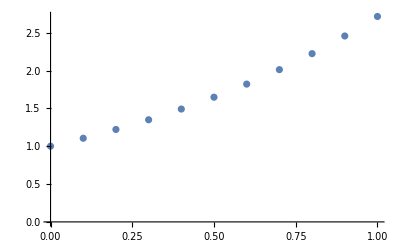

```mathematica
T2Step[f_,ft_,fy_][{h_,t_,y_}]:={h,t+h,y+h f[t,y]+h^2/2(ft[t,y]+fy[t,y]*f[t,y])}

f[t_,y_]:=y
ft[t_,y_]:=0
fy[t_,y_]:=1
h=0.1; t0=0.0; y0=1.0; T2Steps=10;
EulerData=NestList[T2Step[f,ft,fy],{h,t0,y0},T2Steps]
ListPlot[ EulerData⟦All,2;;3⟧]
```

Of course, not everything has such clean derivatives as our simples example!

{{0.1,0.,1.},{0.1,0.1,1.05676},{0.1,0.2,1.12063},{0.1,0.3,1.1936},{0.1,0.4,1.27798},{0.1,0.5,1.37639},{0.1,0.6,1.49143},{0.1,0.7,1.6248},{0.1,0.8,1.77515},{0.1,0.9,1.93445},{0.1,1.,2.08447}}

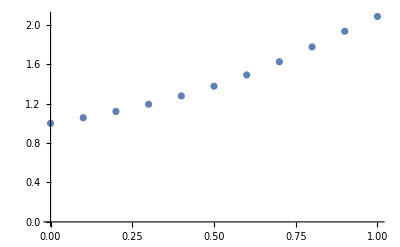

```mathematica
T2Step[f_,ft_,fy_][{h_,t_,y_}]:={h,t+h,y+h f[t,y]+h^2/2(ft[t,y]+fy[t,y]*f[t,y])}

f[t_,y_]:=y Sin[t y]+ Cos[y]
ft[t_,y_]:=y^2 Cos[t y]
fy[t_,y_]:=t y Cos[t y]-Sin[y]+Sin[t y]
h=0.1; t0=0.0; y0=1.0; T2Steps=10;
EulerData=NestList[T2Step[f,ft,fy],{h,t0,y0},T2Steps]
ListPlot[ EulerData⟦All,2;;3⟧]
```

To generate the T# scheme all we need to do is differentiate 
	y''(t)=f_t(t,y(t))+f_y(t,y(t)).f(t,y(t))	
again to get
	y'''=d/dt(f_t+f_y f)=f_tt+f_yt y'+(f_ty+f_yy)f+f_y d/dt(f)=f_tt+f_yt y'+(f_ty+f_yy)f+f_y(f_t+f_y y')=f_tt+f_yt f+(f_ty+f_yy)f+f_y(f_t+f_y f)
this looks like it is rapidly becoming unwieldy!

## Q12:

More transfer orbits.

```mathematica
Md=0.012277471; Ed=1-Md;
TMax=29.4602;
{xSol,ySol}=NDSolveValue[{
r1[t]=√((x[t]+Md)^2+y[t]^2);
r2[t]=√((x[t]-Ed)^2+y[t]^2);
x''[t]==2y'[t]+x[t]-Ed*(x[t]+Md)/r1[t]^3-Md*(x[t]-Ed)/r2[t]^3,
y''[t]==-2x'[t]+y[t]-Ed*y[t]/r1[t]^3-Md*y[t]/r2[t]^3,
x[0]==1.15,
y[0]==0,
x'[0]==0,
y'[0]==0.00868829090
},{x,y},{t, 0, TMax}];
Pic12R=ParametricPlot[ 
{xSol[t],ySol[t]},
{t, 0,TMax}];
Pic12NR=ParametricPlot[ 
{Rot[t].{-Md,0},Rot[t].{Ed,0},Rot[t].{xSol[t],ySol[t]}},
{t, 0,TMax}];
Rot[t_]:=({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}}) 
TabView[{
"Rotating"->Pic12R,
"Non Rotating"->Manipulate[Show[Pic12NR, Epilog->{PointSize[0.03],
{Red,Point[Rot[t].{xSol[t],ySol[t]}]},
{Black,Point[Rot[t].{Ed,0}]}}],
{t,0, TMax}]
}]
```

12

Lets see what the “data” that defines the curves looks like!

```mathematica
xSol["Methods"]
tVals=xSol["Coordinates"]⟦1⟧;
xSol["ValuesOnGrid"];
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid}

```mathematica
ListLogPlot[Table[tVals⟦i+1⟧-tVals⟦i⟧,{i,1,Length[tVals]-1}],PlotRange->All,GridLines->Automatic,Frame->True]
```